```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/610nm.dat"]
```

{{1.12389,0.290727},{1.13423,0.292222},{1.14739,0.289306},{1.16401,0.288332},{1.183,0.291026},{1.20042,0.287432},{1.22646,0.280733},{1.24828,0.276874},{1.27782,0.278313},{1.30453,0.270256},{1.34407,0.270714},{1.38078,0.263594},{1.41705,0.253556},{1.46132,0.245218},{1.51023,0.233094},{1.58758,0.22034},{1.63065,0.214305}}

0.472547-0.156088 x

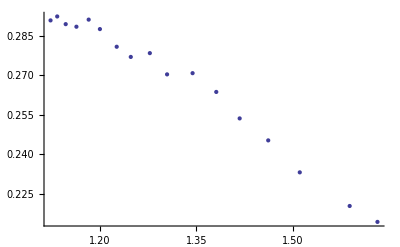

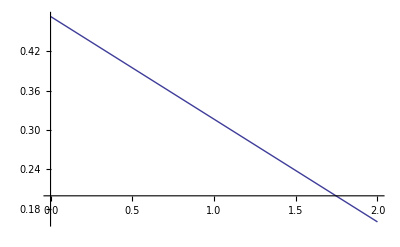

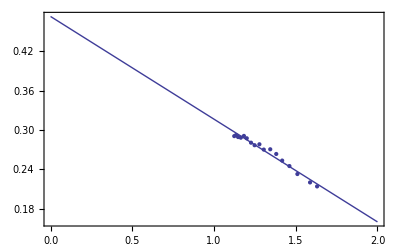

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```